```mathematica
Kc b + Kc (-c)(n-1)+Kc b (n-2)//Simplify
```

(b-c) Kc (-1+n)

```mathematica
XX=(1-Qout)(-c + Kc (-c) + b Kcin )+ (Qin-Qout)(b + Kc b + Kcin (-c)(n-1)+Kcin b (n-2))/.{Kc->-((1-m)^2/n+m^2/(n d-n)),Kcin->-((1-m)^2/n+m^2/(n d -n))}
```

(-c+b (-(1-m)^2/n-m^2/(-n+d n))-c (-(1-m)^2/n-m^2/(-n+d n))) (1-Qout)+(b+b (-(1-m)^2/n-m^2/(-n+d n))+b (-2+n) (-(1-m)^2/n-m^2/(-n+d n))-c (-1+n) (-(1-m)^2/n-m^2/(-n+d n))) (Qin-Qout)

```mathematica
BH=(b + Kc b + Kcin (-c)(n-1)+Kcin b (n-2))/.Kcin->Kc/.{Kc->-((1-m)^2/n+m^2/(n d-n))}//FullSimplify
CH=-(-c + Kc (-c) + b Kcin )/.Kcin->Kc/.{Kc->-((1-m)^2/n+m^2/(n d-n))}//FullSimplify
```

(c (-1+d (-1+m)^2+2 m) (-1+n)+b (-1+2 m+d (1-(-2+m) m (-1+n))-2 m n))/((-1+d) n)

c+((b-c) (-1+d (-1+m)^2+2 m))/((-1+d) n)

```mathematica
prms={b->15,c->1,d->15,n->4}
```

{b→15,c→1,d→15,n→4}

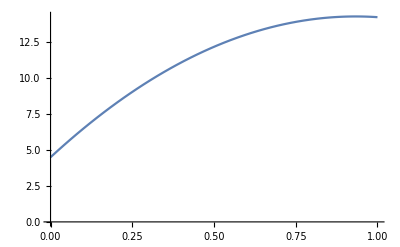

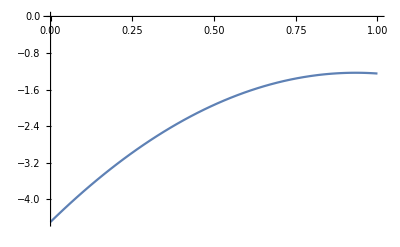

```mathematica
Plot[BH/.prms,{m,0,1},AxesOrigin->{0,0}]
Plot[-CH/.prms,{m,0,1},AxesOrigin->{0,0}]
```

```mathematica
QinM=-((-1+μ) (μ-d μ+m (-1+d μ)))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ));
```

```mathematica
QoutM=(m (-1+μ))/(-(-1+d) μ (1+(-1+n) μ)+m (-1+μ) (1+d (-1+n) μ));
QinWF=(-d+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2));
QoutWF=(-1/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2))/(d (-1+n)+(-1+d)/(1-((1+d (-1+m))^2 (-1+μ)^2)/(-1+d)^2)+1/(2 μ-μ^2));
```

```mathematica
R2M=(Qin-Qout)/(1-Qout)/.{Qin->QinM,Qout->QoutM};
R2WF=(Qin-Qout)/(1-Qout)/.{Qin->QinWF,Qout->QoutWF};
```

```mathematica
R2M//FullSimplify
rrr=Limit[R2M,d->∞]//FullSimplify
Factor[Numerator[rrr]]
FullSimplify[Denominator[rrr]]
```

-((1+d (-1+m)) (-1+μ))/(1+(-1+n) μ+d (-1+m (-1+n) (-1+μ)+μ-n μ))

(-1+m+μ-m μ)/(-1+m (-1+n) (-1+μ)+μ-n μ)

-(-1+m) (-1+μ)

-1+m (-1+n) (-1+μ)+μ-n μ

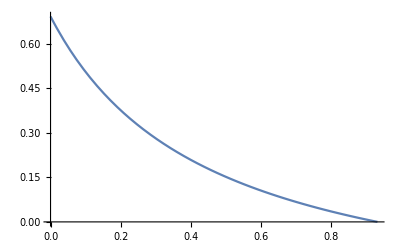

```mathematica
Plot[R2M/.prms/.μ->0.1,{m,0,(d-1)/d/.prms},AxesOrigin->{0,0}]
```

```mathematica
D[R2M,m]//FullSimplify
D[R2WF,m]//FullSimplify
Solve[%==0,m]
```

((-1+d) d n (-1+μ))/(1+(-1+n) μ+d (-1+m (-1+n) (-1+μ)+μ-n μ))^2

(2 (-1+d)^2 d (1+d (-1+m)) n (-1+μ)^2)/(-1+d (2 (1+m (-1+n))+d (-1+(-2+m) m (-1+n)))+2 μ-2 (d (2+d (-1+m)) (-1+m) (-1+n)+n) μ+(1+d (-1+m))^2 (-1+n) μ^2)^2

{{m→(-1+d)/d}}

```mathematica
Collect[XX,{b,c},FullSimplify]
```

1/((-1+d) n)c (-1+n+Qin-n Qin+2 m (1+(-1+n) Qin-n Qout)+d ((-1+n) (-1+Qin)+m^2 (1+(-1+n) Qin-n Qout)+2 m (-1+Qin-n Qin+n Qout)))+(b (1-Qin+2 m (-1+Qin-n Qin+n Qout)+d (-1+Qin+(-2+m) m (-1+Qin-n Qin+n Qout))))/((-1+d) n)

```mathematica
Assuming[c>0,FullSimplify[(XX/.b->0)/-c/.Qout->0]]
```

-(-1+d+2 m-2 d m+d m^2+n-d n+(-1+d (-1+m)^2+2 m) (-1+n) Qin)/((-1+d) n)

```mathematica
β=Qin-(1/n+((n-1)Qin)/n)((1-m)^2+m^2/(d -1))-Qout (2m(1-m)+(d-2)m^2/(d-1))
```

Qin-((1-m)^2+m^2/(-1+d)) (1/n+((-1+n) Qin)/n)-(2 (1-m) m+((-2+d) m^2)/(-1+d)) Qout

```mathematica
bb=Assuming[c>0,FullSimplify[(XX/.c->0)/b]]//FullSimplify
```

(1-Qin+2 m (-1+Qin-n Qin+n Qout)+d (-1+Qin+(-2+m) m (-1+Qin-n Qin+n Qout)))/((-1+d) n)

```mathematica
bb-β//FullSimplify
```

0

```mathematica
γ=1+-(1/n+((n-1)Qin)/n)((1-m)^2+m^2/(d -1))-Qout (2m(1-m)+(d-2)m^2/(d-1))
```

1+((1-m)^2+m^2/(-1+d)) (-1/n-((-1+n) Qin)/n)-(2 (1-m) m+((-2+d) m^2)/(-1+d)) Qout

```mathematica
cc=Assuming[c>0,FullSimplify[(XX/.b->0)/-c]]
```

1/((-1+d) n)((-1+n) (-1+Qin)+2 m (-1+Qin-n Qin+n Qout)+d (-1+n+Qin-n Qin+2 m (1+(-1+n) Qin-n Qout)+m^2 (-1+Qin-n Qin+n Qout)))

```mathematica
cc-γ//FullSimplify
```

0

```mathematica
D[BH,m]//FullSimplify
Solve[%==0]

D[CH,m]//FullSimplify
Solve[%==0]
```

-(2 (b-c) (1+d (-1+m)) (-1+n))/((-1+d) n)

{{c→b},{m→(-1+d)/d},{n→1}}

((b-c) (2+2 d (-1+m)))/((-1+d) n)

{{c→b},{m→(-1+d)/d}}

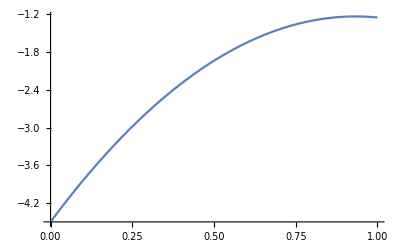

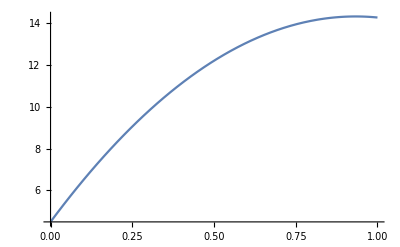

```mathematica
Plot[-CH/.{b->15,c->1,d->15,n->4},{m,0,1}]
Plot[BH/.{b->15,c->1,d->15,n->4},{m,0,1}]
```

## BD

```mathematica
XX=n d(1-Qout)(-c(μ/(n d)^2+1/(n d)(1-μ-din))+b(μ/(n d)^2+1/(n d)(-din)))+n d(b μ/(n d)^2-b din/(n d)+b/(n d (n-1))(1-μ)+(μ/(n d)^2+1/(n d)(-din))(-c))(Qin-Qout)//FullSimplify
```

1/(d (-1+n) n)(b (d n (-din (-1+n) (1+Qin-2 Qout)-(Qin-Qout) (-1+μ))+(-1+n) (1+Qin-2 Qout) μ)+c (-1+n) (-(1+Qin-2 Qout) μ+d n (-1+din (1+Qin-2 Qout)+Qout+μ-Qout μ)))

#### β

```mathematica
βBDD=(1-μ)(eself+(n-1)ein Qin + (n d-n)eout Qout);
```

```mathematica
βBDI=dself eself + (n-1)din ein+(n d -n )dout eout(*
*)+ (n-1)(din eself + dself ein +(n-2)din ein + (n d -n)dout eout)Qin (*
*)+(n d - n)(dself eout + (n-1)din eout + dout eself+(n-1)dout ein+(n d -2n)dout eout)Qout(*
*)-μ/(n d)(1+(n-1)Qin+(n d -n)Qout)(eself+(n-1)ein+(n d-n)eout);
```

#### γ

```mathematica
γBDD=1-μ;
```

```mathematica
γBDI=dself+(n-1)din Qin+(n d-n)dout Qout-μ/(n d)(1+(n-1)Qin+(n d-n)Qout);
```

```mathematica
β=βBDD-βBDI/.{eout->0,ein->1/(n-1),eself->0,dout->(1-n din)/(n d -n),dself->din}//FullSimplify
γ=γBDD-γBDI/.{eout->0,ein->1/(n-1),eself->0,dout->(1-n din)/(n d -n),dself->din}//FullSimplify
```

(d n (din (-1+Qin-n Qin+n Qout)-(Qin-Qout) (-1+μ))+(1+(-1+n) Qin-n Qout) μ)/(d n)

((1+(-1+n) Qin-n Qout) μ-d n (-1+Qout+din (1+(-1+n) Qin-n Qout)+μ-Qout μ))/(d n)

```mathematica
(β - (XX/.c->0))/b//FullSimplify
```

1/(b d n)((d n (din (-1+n) (-1+b+Qin+b Qin-n Qin-2 b Qout+n Qout)+(1+b-n) (Qin-Qout) (-1+μ)))/(-1+n)-(-1+Qin-n Qin+b (1+Qin-2 Qout)+n Qout) μ)

```mathematica
Collect[β,{Qin,Qout},FullSimplify]
```

-din+μ/(d n)+Qout (-1+din n+μ-μ/d)+Qin (1+din-din n+((-1+n-d n) μ)/(d n))

```mathematica
Collect[(XX/.c->0)/b,{Qin,Qout},FullSimplify]
```

-din+μ/(d n)+(Qin (d n (1+din-din n-μ)+(-1+n) μ))/(d (-1+n) n)+(Qout (-2 (-1+n) μ+d n (-1+2 din (-1+n)+μ)))/(d (-1+n) n)

```mathematica
FullSimplify[(-2 (-1+n) μ+d n (-1+2 din (-1+n)+μ))/(d^2 (-1+n) n^2)//Expand]
```

(-2 (-1+n) μ+d n (-1+2 din (-1+n)+μ))/(d^2 (-1+n) n^2)

```mathematica
dWfo=(1-μ)(1/(n d)-1/(n d)^2)-(din/(n d)- 1/(n d)^2);
dWfin=(1-μ)(-1/(n d)^2)-(din/(n d)-1/(n d)^2);

dWself=-c dWfo+b dWfin;
dWin=b/(n-1)dWfo-c dWfin+b(n-2)/(n-1)dWfin;
```

```mathematica
X2=dWself(1-Qout)+dWin (Qin-Qout)(n-1)//FullSimplify
```

1/(d^2 n^2)(b (d n (din (-1+Qin-n Qin+n Qout)-(Qin-Qout) (-1+μ))+(1+(-1+n) Qin-n Qout) μ)+c ((-1+Qin-n Qin+n Qout) μ+d n (-1+Qout+din (1+(-1+n) Qin-n Qout)+μ-Qout μ)))

```mathematica
(β - (n d X2/.c->0))/b//FullSimplify
```

((-1+b) (d n (din (1+(-1+n) Qin-n Qout)+(Qin-Qout) (-1+μ))+(-1+Qin-n Qin+n Qout) μ))/(b d n)

```mathematica
t1=Collect[β,{Qin,Qout},FullSimplify]
t2=Collect[(n d X2/.c->0)/b,{Qin,Qout},FullSimplify]
t1-t2
```

-din+μ/(d n)+Qout (-1+din n+μ-μ/d)+Qin (1+din-din n+((-1+n-d n) μ)/(d n))

-din+μ/(d n)+Qout (-1+din n+μ-μ/d)+Qin (1+din-din n+((-1+n-d n) μ)/(d n))

0

```mathematica
t1=Collect[γ,{Qin,Qout},FullSimplify]
t2=Collect[-(n d X2/.b->0)/c,{Qin,Qout},FullSimplify]
t1-t2
```

1-din+(-1+1/(d n)) μ+Qout (-1+din n+μ-μ/d)+(-1+n) Qin (-din+μ/(d n))

1-din+(-1+1/(d n)) μ+Qout (-1+din n+μ-μ/d)+(-1+n) Qin (-din+μ/(d n))

0

```mathematica
X2
```

((-Qin+b (-1+Qout)+Qout) (d din n-μ)-c (-1+Qout) (-μ+d n (-1+din+μ)))/(d^2 n^2)